```mathematica
<<Combinatorica`
<<GraphUtilities`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

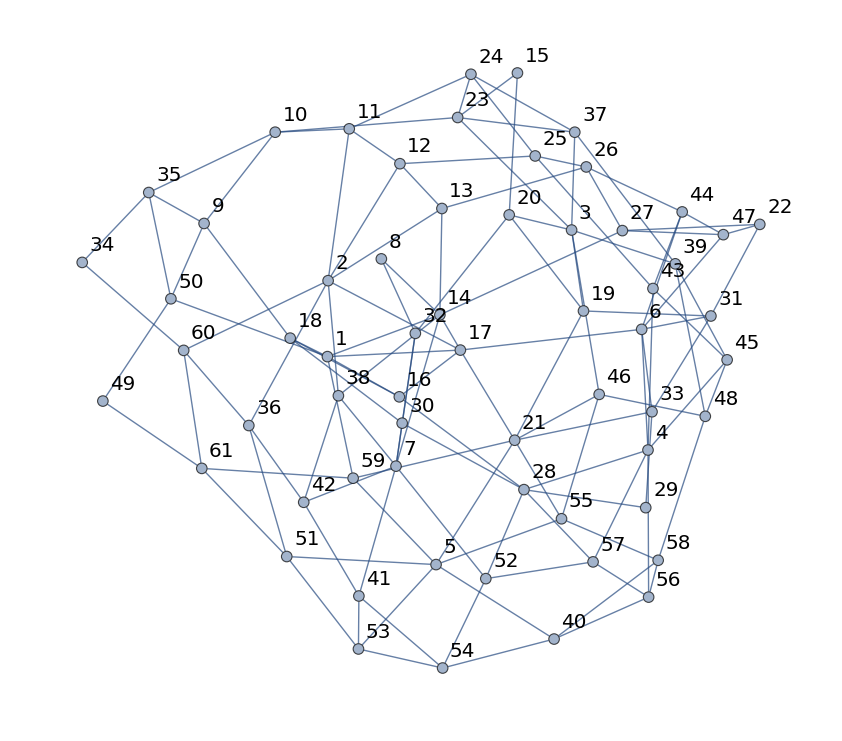

{1,2,2,2,2,3,3,1,3,2,3,3,3,1,3,3,3,2,3,1,1,2,3,1,2,2,3,2,3,1,2,1,1,2,3,1,1,1,3,2,2,2,3,2,3,3,3,3,1,1,1,2,1,2,2,1,1,3,1,3,1}

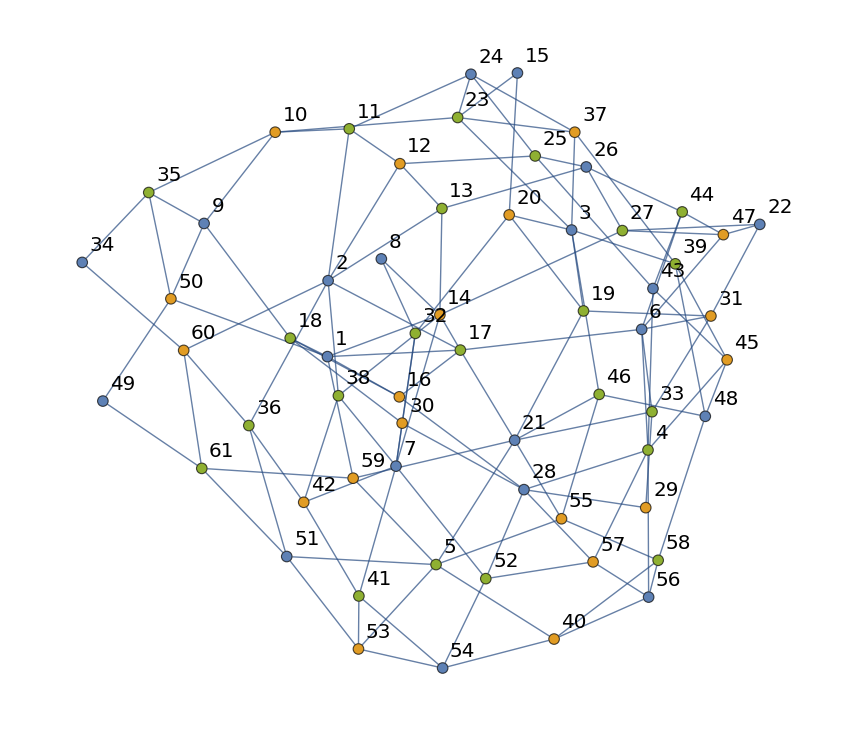

3

{1,14,50,16,59,17,18,2,11,12,36,13,38,3,39,46,19,20,4,56,6,57,5,21,53,47,35,10,23,28,30,7,24,37,25,43,51,26,44,45,55,31,32,40,52,33,41,27,8,15,22,42,9,29,60,34,48,58,54,61,49}

```mathematica
g=System`Graph[{1<->14,1<->50,1<->16,1<->59,1<->17,1<->18,2<->11,2<->12,2<->36,2<->13,2<->38,3<->39,3<->46,3<->19,3<->20,4<->56,4<->6,4<->57,5<->21,5<->53,6<->47,14<->17,17<->2,50<->35,35<->10,10<->23,23<->3,16<->28,28<->4,59<->5,17<->6,18<->30,30<->7,11<->24,24<->37,37<->3,12<->25,25<->43,43<->4,36<->51,51<->5,13<->26,26<->44,44<->6,38<->7,39<->45,45<->4,46<->55,55<->5,19<->31,31<->6,20<->32,32<->7,56<->40,40<->5,57<->52,52<->7,21<->33,33<->6,53<->41,41<->7,47<->27,27<->14,14<->7,8<->14,15<->20,15<->23,22<->31,7<->42,23<->37,22<->47,28<->52,28<->57,21<->59,14<->13,13<->12,12<->11,11<->10,10<->9,20<->19,19<->21,21<->17,17<->16,16<->18,18<->9,23<->24,24<->25,25<->26,26<->27,27<->22,31<->33,33<->29,29<->28,28<->30,30<->32,32<->8,42<->36,36<->60,60<->34,34<->35,35<->9,37<->39,39<->48,48<->58,58<->40,40<->54,54<->41,41<->42,42<->38,38<->14,47<->44,44<->43,43<->45,45<->48,48<->46,46<->21,52<->54,54<->53,53<->51,51<->61,61<->49,49<->50,50<->9,57<->56,56<->58,58<->55,55<->21,59<->61,61<->60,60<->2},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]

GColoredList=MinimumVertexColoring@ToCombinatoricaGraph[g]
GColored=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@GColoredList)]]
Max[GColoredList]
VertexList[GColored]
```